## Successive Strain Replacement

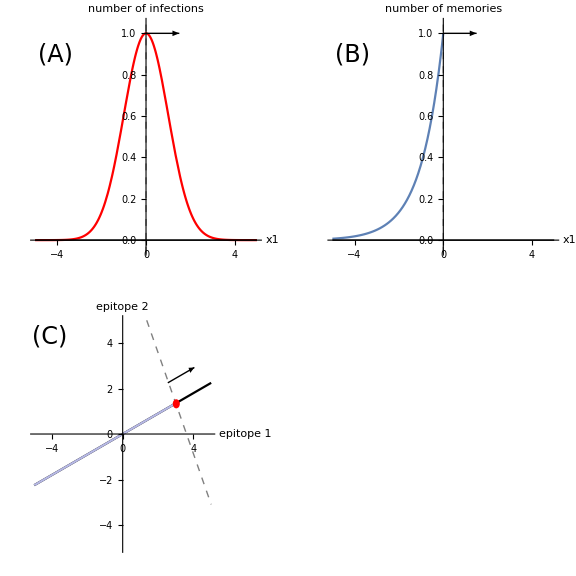

```mathematica
nxt = Plot[Exp[-x^2/2],{x,-5,5}, PlotStyle->Red,PlotRange->{{-5,5},{-.05,1.05}},
AxesLabel->{Style["x1",24,Black],Style["number of infections",24,Black]},
Ticks->None];
hxt = Plot[Exp[x]*UnitStep[-x],{x,-5,0},  PlotRange->{{-5,5},{-.05,1.05}},
AxesLabel->{Style["x1",24,Black],Style["number of memories",24,Black]},
Ticks->None];
vtx = Graphics[{Thick,Dashed,Gray,Line[{{0,-0.2},{0,1.2}}]}];
x1axis = Graphics[{Line[{{-5,0},{5,0}}]}];
directionarrow = Graphics[{Arrow[{{0,1},{1.5,1}}]}];
twodline = Plot[0.45*x*UnitStep[3-x],{x,-5,3},
PlotRange->{{-5,5},{-5,5}},
ColorFunction->Function[{x,y},ColorData["LakeColors"][Exp[-y]]],
AxesStyle->Black,
AspectRatio->1];
twodx1axis = Plot[0.45*x,{x,-5,5},PlotRange->{{-5,5},{-5,5}},PlotStyle->Black, 
AxesLabel->{Style["epitope 1",24,Black], Style["epitope 2",24,Black]},Ticks->False, AspectRatio->1];
twodvtx =  Graphics[{Thick,Dashed,Gray,Line[{{1.358,5},{5,-3.094}}]}];
strainspot = Graphics[{Red,Disk[{3,.45*3},.2]}];
twoddirectionarrow = Graphics[{Arrow[{{2.55,5*.45},{4.05,6.5*.45}}]}];
thelegend = LineLegend[{Red,Blue},{"infections","memory"}];
infectionplot = Show[nxt, vtx,x1axis ,directionarrow,Graphics[Text[Style["(A)",FontSize->24,Black],{-4.1,.9}]]];
memplot = Show[hxt,vtx,x1axis,directionarrow,Graphics[Text[Style["(B)",FontSize->24,Black],{-4.1,.9}]]];
travelingwaveplot = Show[twodx1axis,twodline,twodvtx,strainspot,twoddirectionarrow,Graphics[Text[Style["(C)",FontSize->24,Black],{-4.1,4.3}]]];
infmemcolumn = GraphicsColumn[{infectionplot,memplot}];
Legended[GraphicsGrid[{{infectionplot,travelingwaveplot},{memplot,SpanFromAbove}}], LineLegend[{Red,Blue,Directive[Thick,Dashed,Gray],Black},{"infections","memories","x1=vt","x1 axis"},LabelStyle->{FontSize->24}]];
ssrplot=Show[GraphicsGrid[{{infectionplot,memplot},{travelingwaveplot,LineLegend[{Red,Blue,Directive[Thick,Dashed,Gray], "Black"},{"infections","memories","x1=vt","x1  axis"},LabelStyle->{FontSize->24,Black}]}}],ImageSize->Large]
```